## Setup

```mathematica
Get["FunKit`"]
```

Mathematica package TensorBases loaded

Authors: Andreas Geißel, Franz Richard Sattler

Version: 1.0

Year: 2025

For a list of available bases, call TBInfo[]. For further information on a particular basis, call TBInfo["BasisName"].

This package provides the methods TBGetBasisElement, TBGetInnerProduct, TBGetMetric, TBGetInverseMetric, TBGetProjector for every tensor basis available.

For closer explanations, please call their usage messages, e.g. TBGetProjector::usage.

Other useful tools include TBBasisTransformation, TBVertexTransformation, TBGetIdentityMatrix, TBGetBasisSize, TBGetIndexSet, TBMakePropagator.

To build or manipulate bases, please call TBInfo["BaseBuilder"].

To show information on the used notation, call TBInfo["Notation"].

FormTracer package loaded.

To see all (user-defined and package-defined) FormTracer definitions, call TBInfo["FormTracer"].

Furthermore, TensorBases extends FormTracer. To see all extensions, call TBInfo["Extensions"]

To see all momentum transformations that can be performed by TensorBases, call TBInfo["Momenta"].

Lorentz group undefined, using default names.

Group with name color undefined, using default names.

Group with name flavor undefined, using default names.

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 0.4.0
Year: 2025
For more information and a brief introduction to the package, call FInfo[].
To run the testing suite, you can call  FTest[].

```mathematica
fields= <|
"Commuting"-> {σ[p],Π[p,{f}]},
"Grassmann"->{}
|>;
truncation=<|
GammaN->{
{σ,σ},{Π,Π},
{σ,σ,σ},
{Π,Π,σ},
{σ,σ,σ,σ},
{Π,Π,Π,Π},
{σ,σ,Π,Π}
},
Propagator->{
{σ,σ},{Π,Π}
},
Rdot->{
{σ,σ},{Π,Π}
},
Phidot->{
{σ},
{Π,Π},{σ,σ},
{Π,Π,σ},{σ,σ,σ},
{Π,Π,Π,Π},{σ,σ,σ,σ},{σ,σ,Π,Π}
},
S->{
{Π,Π},{σ,σ},
{Π,Π,Π,Π},{σ,σ,σ,σ},{σ,σ,Π,Π}
}
|>;
setup=<|
"FieldSpace"->fields,
"Truncation"->truncation
|>;
FSetGlobalSetup[setup];
FSetTexStyles[
Phidot->"\\dot{\\Phi}"
];
```

## DSE

In the DSE case, the symmetries can’t be built fully automatically. There are several ways to add the right symmetries to the terms:
First, just put them into the FEx directly:


-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

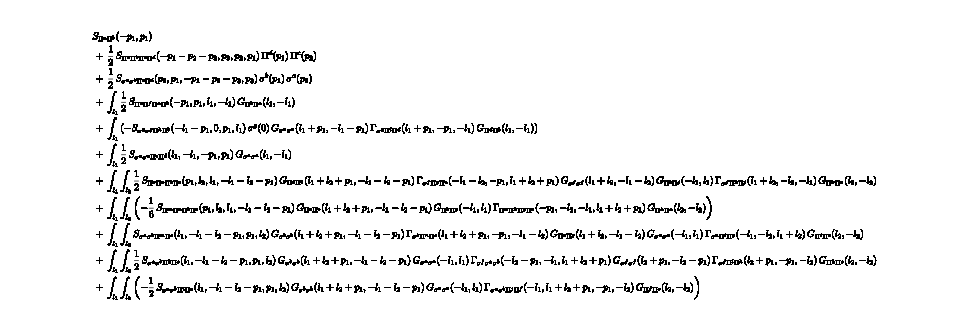

```mathematica
symmetryP2=FMakeSymmetryList[{Π[i1],Π[i2]}];
DSE2P=FEx[FTakeDerivatives[FMakeDSE[Π[i1]],{Π[i2]}],"Symmetries"->symmetryP2]//FTruncate//FPlot//FRoute//FPrint;
```

Another way is to add them as an argument to FTakeDerivatives, or FTruncate:

```mathematica
symmetryP4=FMakeSymmetryList[{Π[i1],Π[i2],Π[i3],Π[i4]}];
DSE4P=FTakeDerivatives[FMakeDSE[Π[i1]],{Π[i2],Π[i3],Π[i4]},"Symmetries"->symmetryP4]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

## fRG

These ones can build their symmetry lists directly:


-Graphics-+-Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
fRG2P=FTakeDerivatives[WetterichEquation,{Π[i1],Π[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

```mathematica
fRG4P=FTakeDerivatives[WetterichEquation,{Π[i1],Π[i2],Π[i3],Π[i4]}]//FTruncate//FPlot//FRoute//FPrint;
```

-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-+-Graphics--Graphics-

-Graphics-

```mathematica
fRG6P=FTakeDerivatives[WetterichEquation,{Π[i1],Π[i2],Π[i3],Π[i4],Π[i5],Π[i6]}]//FTruncate//FPlot//FRoute//FPrint;
```